# Triangle wave

```mathematica
Clear["Global`*"]
```

### Trigonometric Representation

```mathematica
Period=1;
```

```mathematica
Subscript[y, Min]=-1;
```

```mathematica
Subscript[y, Max]=1;
```

```mathematica
f=TriangleWave[{Subscript[y, Min],Subscript[y, Max]},x/Period];
```

```mathematica
fs=FourierTrigSeries[f,x,5,FourierParameters->{1,(2π)/Period}]
```

(8 Sin[2 π x])/π^2-(8 Sin[6 π x])/(9 π^2)+(8 Sin[10 π x])/(25 π^2)

```mathematica
list1=List@@Normal[fs]
```

{(8 Sin[2 π x])/π^2,-(8 Sin[6 π x])/(9 π^2),(8 Sin[10 π x])/(25 π^2)}

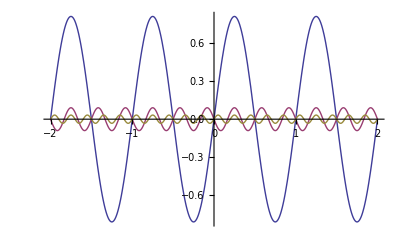

```mathematica
Plot[list1,{x,-2,2},PlotRange->All]
```

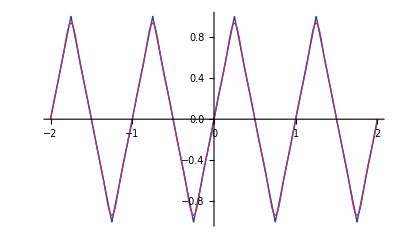

```mathematica
Plot[{f,fs}, {x,-2Period,2Period},PlotRange -> All]
```

### Complex Representation

```mathematica
Clear["Global`*"]
```

The spectral density function

```mathematica
g[k_]:=ⅈ^(k/(2π)-1)32/k^2
```

```mathematica
Table[g[k],{k,2π,20π,4π}]
```

{8/π^2,-8/(9 π^2),8/(25 π^2),-8/(49 π^2),8/(81 π^2)}

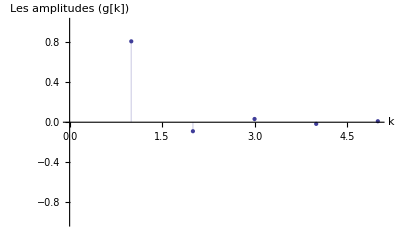

```mathematica
ListPlot[Table[g[k],{k,2π,20π,4π}],Filling->Axis,PlotRange->{-1,1},AxesLabel->{"k","Les amplitudes (g[k])"}]
```

```mathematica
f[x_]=Sum[g[k] ⅇ^(ⅈ  k x),{k,2π,20π,4π}]
```

(8 ⅇ^(2 ⅈ π x))/π^2-(8 ⅇ^(6 ⅈ π x))/(9 π^2)+(8 ⅇ^(10 ⅈ π x))/(25 π^2)-(8 ⅇ^(14 ⅈ π x))/(49 π^2)+(8 ⅇ^(18 ⅈ π x))/(81 π^2)

```mathematica
list2=Table[g[k] ⅇ^(ⅈ k x),{k,2π,20π,4π}]
```

{(8 ⅇ^(2 ⅈ π x))/π^2,-(8 ⅇ^(6 ⅈ π x))/(9 π^2),(8 ⅇ^(10 ⅈ π x))/(25 π^2),-(8 ⅇ^(14 ⅈ π x))/(49 π^2),(8 ⅇ^(18 ⅈ π x))/(81 π^2)}

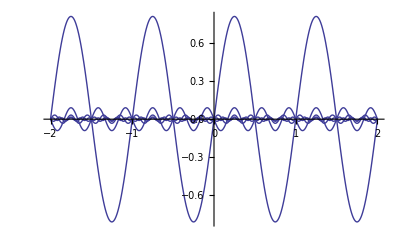

```mathematica
Plot[Im[list2],{x,-2,2},PlotRange->All]
```

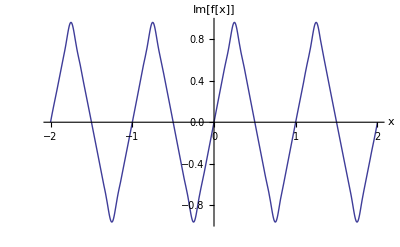

```mathematica
Plot[Im[f[x]],{x,-2,2},AxesLabel->{"x","Im[f[x]]"}]
```

### Play

```mathematica
Play[Im[f[300x]],{x,0,3}]
```

-Graphics-